```mathematica
With[
{max=50000},
Monitor[Table[Chrom5[k],{k,1,max}],{k,N[k/max * 100]}]
]
```

{120,240,480,780,960,1560,1800,960,960,1920,3600,1920,1920,3120,3120,1920,1920,3480,3120,3120,4980,1920,1920,3840,6240,7200,3840,3840,3840,6240,7200,3840,3840,3840,6240,6960,6240,9240,7200,6960,6240,7200,6240,6240,7200,9960,7200,8040,7200,6360,3840,3840,6240,3840,3840,3840,3840,3840,3840,49882,99840,99840,99840,99840,99840,99840,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,99840,99840,99840,99840,99840,99840,99840,99840,99840,99840,99840,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440,61440}
 |  |  |  |

```mathematica
dops25=Map[{Chrom5[#[[1]]],Chrom5[#[[2]]]}&,Take[deps2,{1,50000}]];Length[dops25]
```

50000

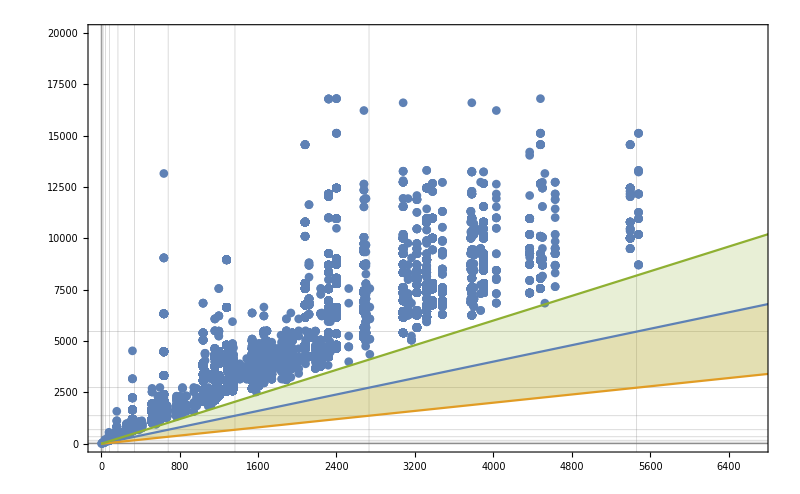

```mathematica
With[
{range=20000},
Show[
ListPlot[dops25/24,PlotRange->{{0,range/3},{0,range}},PlotMarkers->Automatic],
Plot[{x,1/2*x,3/2*x},{x,0,range},  Filling->{2->{1},3->{2}}], Frame->True, GridLines->{Jacobsthal,Jacobsthal},
ImageSize->800
]
]
```

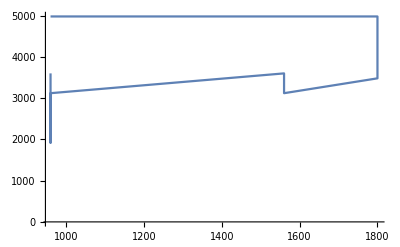

```mathematica
ListLinePlot[DeleteDuplicates[Table[dops25[[i]],{i,Range[10,23]}]]]
```